```mathematica
ClearAll["Global`*"];
(* Natężenie dźwięku w odległości l₁=1m od głośnika (emitującego falę kulistą) wynosi I₁=0.8 W/m.b2. Jaka jest moc głośnika? Jaki jest poziom
natężenia dźwięku L w odległości l₂? Sporządzić wykres zależności L
od l₂ dla l₂ zmieniającego się od 2 m do 10 m. *)
```

```mathematica
Io= 10^-12; (* W/m^2*)
I1= 0.8; (* W/m^2*)
```

```mathematica
l1=1; (*m*)
```

```mathematica
S1=4×π×l1^2;
S2=4×π×l2^2;
```

```mathematica
P=I1× S1 (* W *)
```

10.0531

```mathematica
I2=P/S2;
```

```mathematica
L=10×Log10[I2/Io];
```

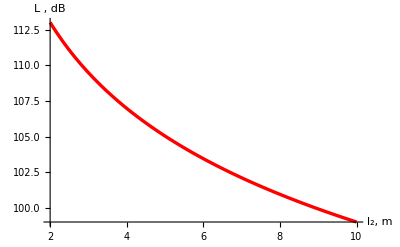

```mathematica
Plot[L,{l2,2,10},
BaseStyle->{FontFamily->"Times",FontSlant->"Italic",FontSize->12},
 PlotStyle->{{RGBColor[1,0,0],Thickness[0.006]}},
AxesLabel->{"l_2, m","L ,  dB"}]
```